# Cuaderno de Prácticas

## MATEMÁTICAS DISCRETAS

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas : 1

### Archivos

```mathematica
indice={
		{"Introducción","Apartado 1","Apartado 2","Apartado 3"},
		{"Capítulo 1: El entorno de trabajo","Generalidades sobre Mathematicas","Interfaz de Usuario"},
		{"Capítulo 2: Aritmética Básica. Variables y Funciones","Operaciones aritméticas elementales"
			,"Tipos de datos y números","Diferentes precisiones en el cálculo"},
		{"Capítulo 3: Polinomio. Cálculos básicos y Divisibilidad",
			"Lista y Representación y formato de una lista","La función Table" ,"Vectores y matrices"},
		{"Capítulo 4: Programación en Mathematica",
			"Expresiones lóghicas y Representaciones gráficas","Órdenes condicionales"
			,"Bucles y estructuras de control"},
		{"Capítulo 5: Lógica proposicional 1: Conectivas y tablas de verdad"
			,"Formas enunciativas y conectivas","Tablas de verdad"},
		{"Capítulo 6: Lógica proposicional 2: Tautologías, contradicciones,formas normales
			, conjuntos adecuados de conectivas, equivalencias e implicaciones lógicas 
				y argumentaciones"
			,"Tautología y contradicción / Equivalencias lógicas e implicaciones lógicas",
			"Formas normales y Argumentaciones válidas","Conjuntos adecuados de conectivas"},
		{"Capítulo 7: Conjuntos y aplicaciones (Partición de un conjunto,Aplicaciones)"
			,"Operaciones con conjuntos","Producto cartesiano","Partes de un conjunto"},
		{"Capítulo 8: Relaciones binarias y conjuntos ordenados","Relaciones binarias",
			"Relaciones de equivalencia","Relaciones de orden y Diagramas de orden o de Hasse"}
};
TextGrid[indice,Frame->All,Spacings->{2,1}]
```

Introducción | Apartado 1 | Apartado 2 | Apartado 3
Capítulo 1: El entorno de trabajo | Generalidades sobre Mathematicas | Interfaz de Usuario | 
Capítulo 2: Aritmética Básica. Variables y Funciones | Operaciones aritméticas elementales | Tipos de datos y números | Diferentes precisiones en el cálculo
Capítulo 3: Polinomio. Cálculos básicos y Divisibilidad | Lista y Representación y formato de una lista | La función Table | Vectores y matrices
Capítulo 4: Programación en Mathematica | Expresiones lóghicas y Representaciones gráficas | Órdenes condicionales | Bucles y estructuras de control
Capítulo 5: Lógica proposicional 1: Conectivas y tablas de verdad | Formas enunciativas y conectivas | Tablas de verdad | 
Capítulo 6: Lógica proposicional 2: Tautologías, contradicciones,formas normales
			, conjuntos adecuados de conectivas, equivalencias e implicaciones lógicas 
				y argumentaciones | Tautología y contradicción / Equivalencias lógicas e implicaciones lógicas | Formas normales y Argumentaciones válidas | Conjuntos adecuados de conectivas
Capítulo 7: Conjuntos y aplicaciones (Partición de un conjunto,Aplicaciones) | Operaciones con conjuntos | Producto cartesiano | Partes de un conjunto
Capítulo 8: Relaciones binarias y conjuntos ordenados | Relaciones binarias | Relaciones de equivalencia | Relaciones de orden y Diagramas de orden o de Hasse

## Práctica I

### Ejercicio I . 6

Texto del ejercicio 1

Solución :

### Ejercicio 2.1

Calcular con 5 y 10 cifras significativas :

a) 3(1+4)-2^2 5-5^(1/5)

```mathematica
N[3(1+4)-2^2 5-5^(1/5),10]
```

-6.379729661

b) 1/2+1/3+1/5

```mathematica
N[1/2+1/3+1/5,10]
```

1.033333333

c) (√5)/3^(1/3)

```mathematica
N[(√5)/3^(1/3),10]
```

1.550402942

i)2^1000

```mathematica
N[2^1000,10]
```

1.071508607×10^301

## Práctica 2

```mathematica
Ejercicio 2.1
```

d) ⅇ^2

```mathematica
N[E^2,10]
```

7.389056099

e) Ln (Cos (π/3))

```mathematica
N[Log[Cos[π/3]],10]
```

-0.6931471806

f) |1/2+1/3-√2 |

```mathematica
N[Abs[1/2+1/3-√2],10]
```

0.580880229

g) Sen(π)+Tan(π)

```mathematica
N[Sin[π]+Tan[π],10]
```

0

h) ArcSin[0.5]-ArcCos[0.5]

```mathematica
N[ArcSin[0.5]-ArcCos[0.5],10]
```

-0.523599

### Ejercicio 2.3

```mathematica
x=26268082;
y=2004;
```

a) Comprobar si x es primo

```mathematica
PrimeQ[x]
```

False

b) Calcular el cociente y el resto de dividir x entre y

```mathematica
Quotient[x,y]
```

13107

```mathematica
Mod[x,y]
```

1654

c) Calcular una aproximación decimal con 20 cifras decimales de la raíz cuadrada de x

```mathematica
N[Sqrt[x],20]
```

5125.2397017115209262

d) Calcular el entero más próximo al número (πy-ⅇ)/x

```mathematica
Round[(π*y-ⅇ)/x]
```

0

e) Calcular el número de Fibonacci del día del mes en que naciste

```mathematica
Fibonacci[6]
```

8

### Ejercicio 3.1

a) Formar una lista con todos los múltiplos de 11 positivos, menores que los dos últimos dígitos del año en que naciste

```mathematica
lista = Select[Range[11,2004,11],#<2004 &]
```

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,561,572,583,594,605,616,627,638,649,660,671,682,693,704,715,726,737,748,759,770,781,792,803,814,825,836,847,858,869,880,891,902,913,924,935,946,957,968,979,990,1001,1012,1023,1034,1045,1056,1067,1078,1089,1100,1111,1122,1133,1144,1155,1166,1177,1188,1199,1210,1221,1232,1243,1254,1265,1276,1287,1298,1309,1320,1331,1342,1353,1364,1375,1386,1397,1408,1419,1430,1441,1452,1463,1474,1485,1496,1507,1518,1529,1540,1551,1562,1573,1584,1595,1606,1617,1628,1639,1650,1661,1672,1683,1694,1705,1716,1727,1738,1749,1760,1771,1782,1793,1804,1815,1826,1837,1848,1859,1870,1881,1892,1903,1914,1925,1936,1947,1958,1969,1980,1991,2002}

```mathematica
Table[i,{i,11,2004,11}]
```

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,561,572,583,594,605,616,627,638,649,660,671,682,693,704,715,726,737,748,759,770,781,792,803,814,825,836,847,858,869,880,891,902,913,924,935,946,957,968,979,990,1001,1012,1023,1034,1045,1056,1067,1078,1089,1100,1111,1122,1133,1144,1155,1166,1177,1188,1199,1210,1221,1232,1243,1254,1265,1276,1287,1298,1309,1320,1331,1342,1353,1364,1375,1386,1397,1408,1419,1430,1441,1452,1463,1474,1485,1496,1507,1518,1529,1540,1551,1562,1573,1584,1595,1606,1617,1628,1639,1650,1661,1672,1683,1694,1705,1716,1727,1738,1749,1760,1771,1782,1793,1804,1815,1826,1837,1848,1859,1870,1881,1892,1903,1914,1925,1936,1947,1958,1969,1980,1991,2002}

```mathematica
Range[11,2004,11]
```

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,561,572,583,594,605,616,627,638,649,660,671,682,693,704,715,726,737,748,759,770,781,792,803,814,825,836,847,858,869,880,891,902,913,924,935,946,957,968,979,990,1001,1012,1023,1034,1045,1056,1067,1078,1089,1100,1111,1122,1133,1144,1155,1166,1177,1188,1199,1210,1221,1232,1243,1254,1265,1276,1287,1298,1309,1320,1331,1342,1353,1364,1375,1386,1397,1408,1419,1430,1441,1452,1463,1474,1485,1496,1507,1518,1529,1540,1551,1562,1573,1584,1595,1606,1617,1628,1639,1650,1661,1672,1683,1694,1705,1716,1727,1738,1749,1760,1771,1782,1793,1804,1815,1826,1837,1848,1859,1870,1881,1892,1903,1914,1925,1936,1947,1958,1969,1980,1991,2002}

```mathematica
Table[i 5,{i,1,5,1}]
```

{5,10,15,20,25}

```mathematica
{5,10,15,20,25}
```

{5,10,15,20,25}

b) Calcular, utilizando el resultado del apartado anterior y las funciones de la tabla 3.1., los múltiplos de 11. entre 15 y 70.

```mathematica
lista;
Select[lista,15<=#<=70&]
```

{22,33,44,55,66}

c) Unir a la lista obtenida en el apartado b), una nueva formada por los múltiplos de 5 entre 10 y 50, pero que en la tercera posición tenga el elemento ϕ. ¿Cuántos elementos tiene la lista que acabamos de conseguir? ¿Cuáles son los elementos que se encuentran en primera, última y octava posición?

```mathematica
multiplosDe5 = Range[10,50,5]
```

{10,15,20,25,30,35,40,45,50}

```mathematica
multiplosDe5Conϕ = Insert[multiplosDe5, ϕ,3]
```

{10,15,ϕ,20,25,30,35,40,45,50}

Unir listas

```mathematica
listaCombinada = Join[lista, multiplosDe5Conϕ]
```

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,561,572,583,594,605,616,627,638,649,660,671,682,693,704,715,726,737,748,759,770,781,792,803,814,825,836,847,858,869,880,891,902,913,924,935,946,957,968,979,990,1001,1012,1023,1034,1045,1056,1067,1078,1089,1100,1111,1122,1133,1144,1155,1166,1177,1188,1199,1210,1221,1232,1243,1254,1265,1276,1287,1298,1309,1320,1331,1342,1353,1364,1375,1386,1397,1408,1419,1430,1441,1452,1463,1474,1485,1496,1507,1518,1529,1540,1551,1562,1573,1584,1595,1606,1617,1628,1639,1650,1661,1672,1683,1694,1705,1716,1727,1738,1749,1760,1771,1782,1793,1804,1815,1826,1837,1848,1859,1870,1881,1892,1903,1914,1925,1936,1947,1958,1969,1980,1991,2002,10,15,ϕ,20,25,30,35,40,45,50}

Determinar el número total de elementos

```mathematica
Length[listaCombinada]
```

192

Obtener la primera, octava y última posición

```mathematica
{First[listaCombinada],Last[listaCombinada],listaCombinada[[8]]}
```

{11,50,88}

### Ejercicio 3.2

Crear una tabla como en el ejercicio 3.4 . cuya primera fila esté formada por los cinco primeros múltiplos positivos del día del mes en que naciste, la segunda fila por sus cubos y la tercera por la potencia quinta de dichos números

```mathematica
tabla=Table[(3*j)^i,{i,1,3},{j,1,5}]
```

{{3,6,9,12,15},{9,36,81,144,225},{27,216,729,1728,3375}}

## Práctica 3

De archivo de practicas el capitulo 4. Cada ejercicio hay que hacerlo con Do, For y While

```mathematica
p=1;
Do[p=p*i,{i,2006,2104,1}]
Do[If[Mod[i,17]==0,p=p*i],{i,2006,2104,1}]
p=1;
For[i=2006, i<= 2104, i= i+17, p=p*i]
For[i=2006, i<= 2104, i= i+17,If[Mod[i,17]==0,p=p*i]]
```

73850604651472793760

```mathematica
Ejercicio 4.3
```

```mathematica
d1d2 = 03;
m1m2 = 06;
anyo = 2004;
anyoPlusMes = anyo*(m1m2 + 6);
```

a) Construir un bucle que nos de todos los múltiplos de D1D2 comprendidos entre el año de tu nacimiento y el año de tu nacimiento multiplicado por M1M2 + 6.

```mathematica
listaAMultiplosFor={};
listaAMultiplosDo = {};
listaAMultiplosWhile={};
For[i=anyo,i<=anyoPlusMes,i++,
	If[Mod[i,d1d2]==0,
		AppendTo[listaAMultiplosFor,i];
	]
]

i = anyo;
While[i <= anyoPlusMes,
  If[Mod[i, d1d2] == 0,
    AppendTo[listaAMultiplosWhile, i]
  ];
  i++;
];
Do[
  If[Mod[i, d1d2] == 0,
    AppendTo[listaAMultiplosDo, i]
  ],
  {i, anyo, anyoPlusMes}
];
If[listaAMultiplosFor === listaAMultiplosWhile === listaAMultiplosDo,
  Print[listaAMultiplosFor]
];
```

{2004,2007,2010,2013,2016,2019,2022,2025,2028,2031,2034,2037,2040,2043,2046,2049,2052,2055,2058,2061,2064,2067,2070,2073,2076,2079,2082,2085,2088,2091,2094,2097,2100,2103,2106,2109,2112,2115,2118,2121,2124,2127,2130,2133,2136,2139,2142,2145,2148,2151,2154,2157,2160,2163,2166,2169,2172,2175,2178,2181,2184,2187,2190,2193,2196,2199,2202,2205,2208,2211,2214,2217,2220,2223,2226,2229,2232,2235,2238,2241,2244,2247,2250,2253,2256,2259,2262,2265,2268,2271,2274,2277,2280,2283,2286,2289,2292,2295,2298,2301,2304,2307,2310,2313,2316,2319,2322,2325,2328,2331,2334,2337,2340,2343,2346,2349,2352,2355,2358,2361,2364,2367,2370,2373,2376,2379,2382,2385,2388,2391,2394,2397,2400,2403,2406,2409,2412,2415,2418,2421,2424,2427,2430,2433,2436,2439,2442,2445,2448,2451,2454,2457,2460,2463,2466,2469,2472,2475,2478,2481,2484,2487,2490,2493,2496,2499,2502,2505,2508,2511,2514,2517,2520,2523,2526,2529,2532,2535,2538,2541,2544,2547,2550,2553,2556,2559,2562,2565,2568,2571,2574,2577,2580,2583,2586,2589,2592,2595,2598,2601,2604,2607,2610,2613,2616,2619,2622,2625,2628,2631,2634,2637,2640,2643,2646,2649,2652,2655,2658,2661,2664,2667,2670,2673,2676,2679,2682,2685,2688,2691,2694,2697,2700,2703,2706,2709,2712,2715,2718,2721,2724,2727,2730,2733,2736,2739,2742,2745,2748,2751,2754,2757,2760,2763,2766,2769,2772,2775,2778,2781,2784,2787,2790,2793,2796,2799,2802,2805,2808,2811,2814,2817,2820,2823,2826,2829,2832,2835,2838,2841,2844,2847,2850,2853,2856,2859,2862,2865,2868,2871,2874,2877,2880,2883,2886,2889,2892,2895,2898,2901,2904,2907,2910,2913,2916,2919,2922,2925,2928,2931,2934,2937,2940,2943,2946,2949,2952,2955,2958,2961,2964,2967,2970,2973,2976,2979,2982,2985,2988,2991,2994,2997,3000,3003,3006,3009,3012,3015,3018,3021,3024,3027,3030,3033,3036,3039,3042,3045,3048,3051,3054,3057,3060,3063,3066,3069,3072,3075,3078,3081,3084,3087,3090,3093,3096,3099,3102,3105,3108,3111,3114,3117,3120,3123,3126,3129,3132,3135,3138,3141,3144,3147,3150,3153,3156,3159,3162,3165,3168,3171,3174,3177,3180,3183,3186,3189,3192,3195,3198,3201,3204,3207,3210,3213,3216,3219,3222,3225,3228,3231,3234,3237,3240,3243,3246,3249,3252,3255,3258,3261,3264,3267,3270,3273,3276,3279,3282,3285,3288,3291,3294,3297,3300,3303,3306,3309,3312,3315,3318,3321,3324,3327,3330,3333,3336,3339,3342,3345,3348,3351,3354,3357,3360,3363,3366,3369,3372,3375,3378,3381,3384,3387,3390,3393,3396,3399,3402,3405,3408,3411,3414,3417,3420,3423,3426,3429,3432,3435,3438,3441,3444,3447,3450,3453,3456,3459,3462,3465,3468,3471,3474,3477,3480,3483,3486,3489,3492,3495,3498,3501,3504,3507,3510,3513,3516,3519,3522,3525,3528,3531,3534,3537,3540,3543,3546,3549,3552,3555,3558,3561,3564,3567,3570,3573,3576,3579,3582,3585,3588,3591,3594,3597,3600,3603,3606,3609,3612,3615,3618,3621,3624,3627,3630,3633,3636,3639,3642,3645,3648,3651,3654,3657,3660,3663,3666,3669,3672,3675,3678,3681,3684,3687,3690,3693,3696,3699,3702,3705,3708,3711,3714,3717,3720,3723,3726,3729,3732,3735,3738,3741,3744,3747,3750,3753,3756,3759,3762,3765,3768,3771,3774,3777,3780,3783,3786,3789,3792,3795,3798,3801,3804,3807,3810,3813,3816,3819,3822,3825,3828,3831,3834,3837,3840,3843,3846,3849,3852,3855,3858,3861,3864,3867,3870,3873,3876,3879,3882,3885,3888,3891,3894,3897,3900,3903,3906,3909,3912,3915,3918,3921,3924,3927,3930,3933,3936,3939,3942,3945,3948,3951,3954,3957,3960,3963,3966,3969,3972,3975,3978,3981,3984,3987,3990,3993,3996,3999,4002,4005,4008,4011,4014,4017,4020,4023,4026,4029,4032,4035,4038,4041,4044,4047,4050,4053,4056,4059,4062,4065,4068,4071,4074,4077,4080,4083,4086,4089,4092,4095,4098,4101,4104,4107,4110,4113,4116,4119,4122,4125,4128,4131,4134,4137,4140,4143,4146,4149,4152,4155,4158,4161,4164,4167,4170,4173,4176,4179,4182,4185,4188,4191,4194,4197,4200,4203,4206,4209,4212,4215,4218,4221,4224,4227,4230,4233,4236,4239,4242,4245,4248,4251,4254,4257,4260,4263,4266,4269,4272,4275,4278,4281,4284,4287,4290,4293,4296,4299,4302,4305,4308,4311,4314,4317,4320,4323,4326,4329,4332,4335,4338,4341,4344,4347,4350,4353,4356,4359,4362,4365,4368,4371,4374,4377,4380,4383,4386,4389,4392,4395,4398,4401,4404,4407,4410,4413,4416,4419,4422,4425,4428,4431,4434,4437,4440,4443,4446,4449,4452,4455,4458,4461,4464,4467,4470,4473,4476,4479,4482,4485,4488,4491,4494,4497,4500,4503,4506,4509,4512,4515,4518,4521,4524,4527,4530,4533,4536,4539,4542,4545,4548,4551,4554,4557,4560,4563,4566,4569,4572,4575,4578,4581,4584,4587,4590,4593,4596,4599,4602,4605,4608,4611,4614,4617,4620,4623,4626,4629,4632,4635,4638,4641,4644,4647,4650,4653,4656,4659,4662,4665,4668,4671,4674,4677,4680,4683,4686,4689,4692,4695,4698,4701,4704,4707,4710,4713,4716,4719,4722,4725,4728,4731,4734,4737,4740,4743,4746,4749,4752,4755,4758,4761,4764,4767,4770,4773,4776,4779,4782,4785,4788,4791,4794,4797,4800,4803,4806,4809,4812,4815,4818,4821,4824,4827,4830,4833,4836,4839,4842,4845,4848,4851,4854,4857,4860,4863,4866,4869,4872,4875,4878,4881,4884,4887,4890,4893,4896,4899,4902,4905,4908,4911,4914,4917,4920,4923,4926,4929,4932,4935,4938,4941,4944,4947,4950,4953,4956,4959,4962,4965,4968,4971,4974,4977,4980,4983,4986,4989,4992,4995,4998,5001,5004,5007,5010,5013,5016,5019,5022,5025,5028,5031,5034,5037,5040,5043,5046,5049,5052,5055,5058,5061,5064,5067,5070,5073,5076,5079,5082,5085,5088,5091,5094,5097,5100,5103,5106,5109,5112,5115,5118,5121,5124,5127,5130,5133,5136,5139,5142,5145,5148,5151,5154,5157,5160,5163,5166,5169,5172,5175,5178,5181,5184,5187,5190,5193,5196,5199,5202,5205,5208,5211,5214,5217,5220,5223,5226,5229,5232,5235,5238,5241,5244,5247,5250,5253,5256,5259,5262,5265,5268,5271,5274,5277,5280,5283,5286,5289,5292,5295,5298,5301,5304,5307,5310,5313,5316,5319,5322,5325,5328,5331,5334,5337,5340,5343,5346,5349,5352,5355,5358,5361,5364,5367,5370,5373,5376,5379,5382,5385,5388,5391,5394,5397,5400,5403,5406,5409,5412,5415,5418,5421,5424,5427,5430,5433,5436,5439,5442,5445,5448,5451,5454,5457,5460,5463,5466,5469,5472,5475,5478,5481,5484,5487,5490,5493,5496,5499,5502,5505,5508,5511,5514,5517,5520,5523,5526,5529,5532,5535,5538,5541,5544,5547,5550,5553,5556,5559,5562,5565,5568,5571,5574,5577,5580,5583,5586,5589,5592,5595,5598,5601,5604,5607,5610,5613,5616,5619,5622,5625,5628,5631,5634,5637,5640,5643,5646,5649,5652,5655,5658,5661,5664,5667,5670,5673,5676,5679,5682,5685,5688,5691,5694,5697,5700,5703,5706,5709,5712,5715,5718,5721,5724,5727,5730,5733,5736,5739,5742,5745,5748,5751,5754,5757,5760,5763,5766,5769,5772,5775,5778,5781,5784,5787,5790,5793,5796,5799,5802,5805,5808,5811,5814,5817,5820,5823,5826,5829,5832,5835,5838,5841,5844,5847,5850,5853,5856,5859,5862,5865,5868,5871,5874,5877,5880,5883,5886,5889,5892,5895,5898,5901,5904,5907,5910,5913,5916,5919,5922,5925,5928,5931,5934,5937,5940,5943,5946,5949,5952,5955,5958,5961,5964,5967,5970,5973,5976,5979,5982,5985,5988,5991,5994,5997,6000,6003,6006,6009,6012,6015,6018,6021,6024,6027,6030,6033,6036,6039,6042,6045,6048,6051,6054,6057,6060,6063,6066,6069,6072,6075,6078,6081,6084,6087,6090,6093,6096,6099,6102,6105,6108,6111,6114,6117,6120,6123,6126,6129,6132,6135,6138,6141,6144,6147,6150,6153,6156,6159,6162,6165,6168,6171,6174,6177,6180,6183,6186,6189,6192,6195,6198,6201,6204,6207,6210,6213,6216,6219,6222,6225,6228,6231,6234,6237,6240,6243,6246,6249,6252,6255,6258,6261,6264,6267,6270,6273,6276,6279,6282,6285,6288,6291,6294,6297,6300,6303,6306,6309,6312,6315,6318,6321,6324,6327,6330,6333,6336,6339,6342,6345,6348,6351,6354,6357,6360,6363,6366,6369,6372,6375,6378,6381,6384,6387,6390,6393,6396,6399,6402,6405,6408,6411,6414,6417,6420,6423,6426,6429,6432,6435,6438,6441,6444,6447,6450,6453,6456,6459,6462,6465,6468,6471,6474,6477,6480,6483,6486,6489,6492,6495,6498,6501,6504,6507,6510,6513,6516,6519,6522,6525,6528,6531,6534,6537,6540,6543,6546,6549,6552,6555,6558,6561,6564,6567,6570,6573,6576,6579,6582,6585,6588,6591,6594,6597,6600,6603,6606,6609,6612,6615,6618,6621,6624,6627,6630,6633,6636,6639,6642,6645,6648,6651,6654,6657,6660,6663,6666,6669,6672,6675,6678,6681,6684,6687,6690,6693,6696,6699,6702,6705,6708,6711,6714,6717,6720,6723,6726,6729,6732,6735,6738,6741,6744,6747,6750,6753,6756,6759,6762,6765,6768,6771,6774,6777,6780,6783,6786,6789,6792,6795,6798,6801,6804,6807,6810,6813,6816,6819,6822,6825,6828,6831,6834,6837,6840,6843,6846,6849,6852,6855,6858,6861,6864,6867,6870,6873,6876,6879,6882,6885,6888,6891,6894,6897,6900,6903,6906,6909,6912,6915,6918,6921,6924,6927,6930,6933,6936,6939,6942,6945,6948,6951,6954,6957,6960,6963,6966,6969,6972,6975,6978,6981,6984,6987,6990,6993,6996,6999,7002,7005,7008,7011,7014,7017,7020,7023,7026,7029,7032,7035,7038,7041,7044,7047,7050,7053,7056,7059,7062,7065,7068,7071,7074,7077,7080,7083,7086,7089,7092,7095,7098,7101,7104,7107,7110,7113,7116,7119,7122,7125,7128,7131,7134,7137,7140,7143,7146,7149,7152,7155,7158,7161,7164,7167,7170,7173,7176,7179,7182,7185,7188,7191,7194,7197,7200,7203,7206,7209,7212,7215,7218,7221,7224,7227,7230,7233,7236,7239,7242,7245,7248,7251,7254,7257,7260,7263,7266,7269,7272,7275,7278,7281,7284,7287,7290,7293,7296,7299,7302,7305,7308,7311,7314,7317,7320,7323,7326,7329,7332,7335,7338,7341,7344,7347,7350,7353,7356,7359,7362,7365,7368,7371,7374,7377,7380,7383,7386,7389,7392,7395,7398,7401,7404,7407,7410,7413,7416,7419,7422,7425,7428,7431,7434,7437,7440,7443,7446,7449,7452,7455,7458,7461,7464,7467,7470,7473,7476,7479,7482,7485,7488,7491,7494,7497,7500,7503,7506,7509,7512,7515,7518,7521,7524,7527,7530,7533,7536,7539,7542,7545,7548,7551,7554,7557,7560,7563,7566,7569,7572,7575,7578,7581,7584,7587,7590,7593,7596,7599,7602,7605,7608,7611,7614,7617,7620,7623,7626,7629,7632,7635,7638,7641,7644,7647,7650,7653,7656,7659,7662,7665,7668,7671,7674,7677,7680,7683,7686,7689,7692,7695,7698,7701,7704,7707,7710,7713,7716,7719,7722,7725,7728,7731,7734,7737,7740,7743,7746,7749,7752,7755,7758,7761,7764,7767,7770,7773,7776,7779,7782,7785,7788,7791,7794,7797,7800,7803,7806,7809,7812,7815,7818,7821,7824,7827,7830,7833,7836,7839,7842,7845,7848,7851,7854,7857,7860,7863,7866,7869,7872,7875,7878,7881,7884,7887,7890,7893,7896,7899,7902,7905,7908,7911,7914,7917,7920,7923,7926,7929,7932,7935,7938,7941,7944,7947,7950,7953,7956,7959,7962,7965,7968,7971,7974,7977,7980,7983,7986,7989,7992,7995,7998,8001,8004,8007,8010,8013,8016,8019,8022,8025,8028,8031,8034,8037,8040,8043,8046,8049,8052,8055,8058,8061,8064,8067,8070,8073,8076,8079,8082,8085,8088,8091,8094,8097,8100,8103,8106,8109,8112,8115,8118,8121,8124,8127,8130,8133,8136,8139,8142,8145,8148,8151,8154,8157,8160,8163,8166,8169,8172,8175,8178,8181,8184,8187,8190,8193,8196,8199,8202,8205,8208,8211,8214,8217,8220,8223,8226,8229,8232,8235,8238,8241,8244,8247,8250,8253,8256,8259,8262,8265,8268,8271,8274,8277,8280,8283,8286,8289,8292,8295,8298,8301,8304,8307,8310,8313,8316,8319,8322,8325,8328,8331,8334,8337,8340,8343,8346,8349,8352,8355,8358,8361,8364,8367,8370,8373,8376,8379,8382,8385,8388,8391,8394,8397,8400,8403,8406,8409,8412,8415,8418,8421,8424,8427,8430,8433,8436,8439,8442,8445,8448,8451,8454,8457,8460,8463,8466,8469,8472,8475,8478,8481,8484,8487,8490,8493,8496,8499,8502,8505,8508,8511,8514,8517,8520,8523,8526,8529,8532,8535,8538,8541,8544,8547,8550,8553,8556,8559,8562,8565,8568,8571,8574,8577,8580,8583,8586,8589,8592,8595,8598,8601,8604,8607,8610,8613,8616,8619,8622,8625,8628,8631,8634,8637,8640,8643,8646,8649,8652,8655,8658,8661,8664,8667,8670,8673,8676,8679,8682,8685,8688,8691,8694,8697,8700,8703,8706,8709,8712,8715,8718,8721,8724,8727,8730,8733,8736,8739,8742,8745,8748,8751,8754,8757,8760,8763,8766,8769,8772,8775,8778,8781,8784,8787,8790,8793,8796,8799,8802,8805,8808,8811,8814,8817,8820,8823,8826,8829,8832,8835,8838,8841,8844,8847,8850,8853,8856,8859,8862,8865,8868,8871,8874,8877,8880,8883,8886,8889,8892,8895,8898,8901,8904,8907,8910,8913,8916,8919,8922,8925,8928,8931,8934,8937,8940,8943,8946,8949,8952,8955,8958,8961,8964,8967,8970,8973,8976,8979,8982,8985,8988,8991,8994,8997,9000,9003,9006,9009,9012,9015,9018,9021,9024,9027,9030,9033,9036,9039,9042,9045,9048,9051,9054,9057,9060,9063,9066,9069,9072,9075,9078,9081,9084,9087,9090,9093,9096,9099,9102,9105,9108,9111,9114,9117,9120,9123,9126,9129,9132,9135,9138,9141,9144,9147,9150,9153,9156,9159,9162,9165,9168,9171,9174,9177,9180,9183,9186,9189,9192,9195,9198,9201,9204,9207,9210,9213,9216,9219,9222,9225,9228,9231,9234,9237,9240,9243,9246,9249,9252,9255,9258,9261,9264,9267,9270,9273,9276,9279,9282,9285,9288,9291,9294,9297,9300,9303,9306,9309,9312,9315,9318,9321,9324,9327,9330,9333,9336,9339,9342,9345,9348,9351,9354,9357,9360,9363,9366,9369,9372,9375,9378,9381,9384,9387,9390,9393,9396,9399,9402,9405,9408,9411,9414,9417,9420,9423,9426,9429,9432,9435,9438,9441,9444,9447,9450,9453,9456,9459,9462,9465,9468,9471,9474,9477,9480,9483,9486,9489,9492,9495,9498,9501,9504,9507,9510,9513,9516,9519,9522,9525,9528,9531,9534,9537,9540,9543,9546,9549,9552,9555,9558,9561,9564,9567,9570,9573,9576,9579,9582,9585,9588,9591,9594,9597,9600,9603,9606,9609,9612,9615,9618,9621,9624,9627,9630,9633,9636,9639,9642,9645,9648,9651,9654,9657,9660,9663,9666,9669,9672,9675,9678,9681,9684,9687,9690,9693,9696,9699,9702,9705,9708,9711,9714,9717,9720,9723,9726,9729,9732,9735,9738,9741,9744,9747,9750,9753,9756,9759,9762,9765,9768,9771,9774,9777,9780,9783,9786,9789,9792,9795,9798,9801,9804,9807,9810,9813,9816,9819,9822,9825,9828,9831,9834,9837,9840,9843,9846,9849,9852,9855,9858,9861,9864,9867,9870,9873,9876,9879,9882,9885,9888,9891,9894,9897,9900,9903,9906,9909,9912,9915,9918,9921,9924,9927,9930,9933,9936,9939,9942,9945,9948,9951,9954,9957,9960,9963,9966,9969,9972,9975,9978,9981,9984,9987,9990,9993,9996,9999,10002,10005,10008,10011,10014,10017,10020,10023,10026,10029,10032,10035,10038,10041,10044,10047,10050,10053,10056,10059,10062,10065,10068,10071,10074,10077,10080,10083,10086,10089,10092,10095,10098,10101,10104,10107,10110,10113,10116,10119,10122,10125,10128,10131,10134,10137,10140,10143,10146,10149,10152,10155,10158,10161,10164,10167,10170,10173,10176,10179,10182,10185,10188,10191,10194,10197,10200,10203,10206,10209,10212,10215,10218,10221,10224,10227,10230,10233,10236,10239,10242,10245,10248,10251,10254,10257,10260,10263,10266,10269,10272,10275,10278,10281,10284,10287,10290,10293,10296,10299,10302,10305,10308,10311,10314,10317,10320,10323,10326,10329,10332,10335,10338,10341,10344,10347,10350,10353,10356,10359,10362,10365,10368,10371,10374,10377,10380,10383,10386,10389,10392,10395,10398,10401,10404,10407,10410,10413,10416,10419,10422,10425,10428,10431,10434,10437,10440,10443,10446,10449,10452,10455,10458,10461,10464,10467,10470,10473,10476,10479,10482,10485,10488,10491,10494,10497,10500,10503,10506,10509,10512,10515,10518,10521,10524,10527,10530,10533,10536,10539,10542,10545,10548,10551,10554,10557,10560,10563,10566,10569,10572,10575,10578,10581,10584,10587,10590,10593,10596,10599,10602,10605,10608,10611,10614,10617,10620,10623,10626,10629,10632,10635,10638,10641,10644,10647,10650,10653,10656,10659,10662,10665,10668,10671,10674,10677,10680,10683,10686,10689,10692,10695,10698,10701,10704,10707,10710,10713,10716,10719,10722,10725,10728,10731,10734,10737,10740,10743,10746,10749,10752,10755,10758,10761,10764,10767,10770,10773,10776,10779,10782,10785,10788,10791,10794,10797,10800,10803,10806,10809,10812,10815,10818,10821,10824,10827,10830,10833,10836,10839,10842,10845,10848,10851,10854,10857,10860,10863,10866,10869,10872,10875,10878,10881,10884,10887,10890,10893,10896,10899,10902,10905,10908,10911,10914,10917,10920,10923,10926,10929,10932,10935,10938,10941,10944,10947,10950,10953,10956,10959,10962,10965,10968,10971,10974,10977,10980,10983,10986,10989,10992,10995,10998,11001,11004,11007,11010,11013,11016,11019,11022,11025,11028,11031,11034,11037,11040,11043,11046,11049,11052,11055,11058,11061,11064,11067,11070,11073,11076,11079,11082,11085,11088,11091,11094,11097,11100,11103,11106,11109,11112,11115,11118,11121,11124,11127,11130,11133,11136,11139,11142,11145,11148,11151,11154,11157,11160,11163,11166,11169,11172,11175,11178,11181,11184,11187,11190,11193,11196,11199,11202,11205,11208,11211,11214,11217,11220,11223,11226,11229,11232,11235,11238,11241,11244,11247,11250,11253,11256,11259,11262,11265,11268,11271,11274,11277,11280,11283,11286,11289,11292,11295,11298,11301,11304,11307,11310,11313,11316,11319,11322,11325,11328,11331,11334,11337,11340,11343,11346,11349,11352,11355,11358,11361,11364,11367,11370,11373,11376,11379,11382,11385,11388,11391,11394,11397,11400,11403,11406,11409,11412,11415,11418,11421,11424,11427,11430,11433,11436,11439,11442,11445,11448,11451,11454,11457,11460,11463,11466,11469,11472,11475,11478,11481,11484,11487,11490,11493,11496,11499,11502,11505,11508,11511,11514,11517,11520,11523,11526,11529,11532,11535,11538,11541,11544,11547,11550,11553,11556,11559,11562,11565,11568,11571,11574,11577,11580,11583,11586,11589,11592,11595,11598,11601,11604,11607,11610,11613,11616,11619,11622,11625,11628,11631,11634,11637,11640,11643,11646,11649,11652,11655,11658,11661,11664,11667,11670,11673,11676,11679,11682,11685,11688,11691,11694,11697,11700,11703,11706,11709,11712,11715,11718,11721,11724,11727,11730,11733,11736,11739,11742,11745,11748,11751,11754,11757,11760,11763,11766,11769,11772,11775,11778,11781,11784,11787,11790,11793,11796,11799,11802,11805,11808,11811,11814,11817,11820,11823,11826,11829,11832,11835,11838,11841,11844,11847,11850,11853,11856,11859,11862,11865,11868,11871,11874,11877,11880,11883,11886,11889,11892,11895,11898,11901,11904,11907,11910,11913,11916,11919,11922,11925,11928,11931,11934,11937,11940,11943,11946,11949,11952,11955,11958,11961,11964,11967,11970,11973,11976,11979,11982,11985,11988,11991,11994,11997,12000,12003,12006,12009,12012,12015,12018,12021,12024,12027,12030,12033,12036,12039,12042,12045,12048,12051,12054,12057,12060,12063,12066,12069,12072,12075,12078,12081,12084,12087,12090,12093,12096,12099,12102,12105,12108,12111,12114,12117,12120,12123,12126,12129,12132,12135,12138,12141,12144,12147,12150,12153,12156,12159,12162,12165,12168,12171,12174,12177,12180,12183,12186,12189,12192,12195,12198,12201,12204,12207,12210,12213,12216,12219,12222,12225,12228,12231,12234,12237,12240,12243,12246,12249,12252,12255,12258,12261,12264,12267,12270,12273,12276,12279,12282,12285,12288,12291,12294,12297,12300,12303,12306,12309,12312,12315,12318,12321,12324,12327,12330,12333,12336,12339,12342,12345,12348,12351,12354,12357,12360,12363,12366,12369,12372,12375,12378,12381,12384,12387,12390,12393,12396,12399,12402,12405,12408,12411,12414,12417,12420,12423,12426,12429,12432,12435,12438,12441,12444,12447,12450,12453,12456,12459,12462,12465,12468,12471,12474,12477,12480,12483,12486,12489,12492,12495,12498,12501,12504,12507,12510,12513,12516,12519,12522,12525,12528,12531,12534,12537,12540,12543,12546,12549,12552,12555,12558,12561,12564,12567,12570,12573,12576,12579,12582,12585,12588,12591,12594,12597,12600,12603,12606,12609,12612,12615,12618,12621,12624,12627,12630,12633,12636,12639,12642,12645,12648,12651,12654,12657,12660,12663,12666,12669,12672,12675,12678,12681,12684,12687,12690,12693,12696,12699,12702,12705,12708,12711,12714,12717,12720,12723,12726,12729,12732,12735,12738,12741,12744,12747,12750,12753,12756,12759,12762,12765,12768,12771,12774,12777,12780,12783,12786,12789,12792,12795,12798,12801,12804,12807,12810,12813,12816,12819,12822,12825,12828,12831,12834,12837,12840,12843,12846,12849,12852,12855,12858,12861,12864,12867,12870,12873,12876,12879,12882,12885,12888,12891,12894,12897,12900,12903,12906,12909,12912,12915,12918,12921,12924,12927,12930,12933,12936,12939,12942,12945,12948,12951,12954,12957,12960,12963,12966,12969,12972,12975,12978,12981,12984,12987,12990,12993,12996,12999,13002,13005,13008,13011,13014,13017,13020,13023,13026,13029,13032,13035,13038,13041,13044,13047,13050,13053,13056,13059,13062,13065,13068,13071,13074,13077,13080,13083,13086,13089,13092,13095,13098,13101,13104,13107,13110,13113,13116,13119,13122,13125,13128,13131,13134,13137,13140,13143,13146,13149,13152,13155,13158,13161,13164,13167,13170,13173,13176,13179,13182,13185,13188,13191,13194,13197,13200,13203,13206,13209,13212,13215,13218,13221,13224,13227,13230,13233,13236,13239,13242,13245,13248,13251,13254,13257,13260,13263,13266,13269,13272,13275,13278,13281,13284,13287,13290,13293,13296,13299,13302,13305,13308,13311,13314,13317,13320,13323,13326,13329,13332,13335,13338,13341,13344,13347,13350,13353,13356,13359,13362,13365,13368,13371,13374,13377,13380,13383,13386,13389,13392,13395,13398,13401,13404,13407,13410,13413,13416,13419,13422,13425,13428,13431,13434,13437,13440,13443,13446,13449,13452,13455,13458,13461,13464,13467,13470,13473,13476,13479,13482,13485,13488,13491,13494,13497,13500,13503,13506,13509,13512,13515,13518,13521,13524,13527,13530,13533,13536,13539,13542,13545,13548,13551,13554,13557,13560,13563,13566,13569,13572,13575,13578,13581,13584,13587,13590,13593,13596,13599,13602,13605,13608,13611,13614,13617,13620,13623,13626,13629,13632,13635,13638,13641,13644,13647,13650,13653,13656,13659,13662,13665,13668,13671,13674,13677,13680,13683,13686,13689,13692,13695,13698,13701,13704,13707,13710,13713,13716,13719,13722,13725,13728,13731,13734,13737,13740,13743,13746,13749,13752,13755,13758,13761,13764,13767,13770,13773,13776,13779,13782,13785,13788,13791,13794,13797,13800,13803,13806,13809,13812,13815,13818,13821,13824,13827,13830,13833,13836,13839,13842,13845,13848,13851,13854,13857,13860,13863,13866,13869,13872,13875,13878,13881,13884,13887,13890,13893,13896,13899,13902,13905,13908,13911,13914,13917,13920,13923,13926,13929,13932,13935,13938,13941,13944,13947,13950,13953,13956,13959,13962,13965,13968,13971,13974,13977,13980,13983,13986,13989,13992,13995,13998,14001,14004,14007,14010,14013,14016,14019,14022,14025,14028,14031,14034,14037,14040,14043,14046,14049,14052,14055,14058,14061,14064,14067,14070,14073,14076,14079,14082,14085,14088,14091,14094,14097,14100,14103,14106,14109,14112,14115,14118,14121,14124,14127,14130,14133,14136,14139,14142,14145,14148,14151,14154,14157,14160,14163,14166,14169,14172,14175,14178,14181,14184,14187,14190,14193,14196,14199,14202,14205,14208,14211,14214,14217,14220,14223,14226,14229,14232,14235,14238,14241,14244,14247,14250,14253,14256,14259,14262,14265,14268,14271,14274,14277,14280,14283,14286,14289,14292,14295,14298,14301,14304,14307,14310,14313,14316,14319,14322,14325,14328,14331,14334,14337,14340,14343,14346,14349,14352,14355,14358,14361,14364,14367,14370,14373,14376,14379,14382,14385,14388,14391,14394,14397,14400,14403,14406,14409,14412,14415,14418,14421,14424,14427,14430,14433,14436,14439,14442,14445,14448,14451,14454,14457,14460,14463,14466,14469,14472,14475,14478,14481,14484,14487,14490,14493,14496,14499,14502,14505,14508,14511,14514,14517,14520,14523,14526,14529,14532,14535,14538,14541,14544,14547,14550,14553,14556,14559,14562,14565,14568,14571,14574,14577,14580,14583,14586,14589,14592,14595,14598,14601,14604,14607,14610,14613,14616,14619,14622,14625,14628,14631,14634,14637,14640,14643,14646,14649,14652,14655,14658,14661,14664,14667,14670,14673,14676,14679,14682,14685,14688,14691,14694,14697,14700,14703,14706,14709,14712,14715,14718,14721,14724,14727,14730,14733,14736,14739,14742,14745,14748,14751,14754,14757,14760,14763,14766,14769,14772,14775,14778,14781,14784,14787,14790,14793,14796,14799,14802,14805,14808,14811,14814,14817,14820,14823,14826,14829,14832,14835,14838,14841,14844,14847,14850,14853,14856,14859,14862,14865,14868,14871,14874,14877,14880,14883,14886,14889,14892,14895,14898,14901,14904,14907,14910,14913,14916,14919,14922,14925,14928,14931,14934,14937,14940,14943,14946,14949,14952,14955,14958,14961,14964,14967,14970,14973,14976,14979,14982,14985,14988,14991,14994,14997,15000,15003,15006,15009,15012,15015,15018,15021,15024,15027,15030,15033,15036,15039,15042,15045,15048,15051,15054,15057,15060,15063,15066,15069,15072,15075,15078,15081,15084,15087,15090,15093,15096,15099,15102,15105,15108,15111,15114,15117,15120,15123,15126,15129,15132,15135,15138,15141,15144,15147,15150,15153,15156,15159,15162,15165,15168,15171,15174,15177,15180,15183,15186,15189,15192,15195,15198,15201,15204,15207,15210,15213,15216,15219,15222,15225,15228,15231,15234,15237,15240,15243,15246,15249,15252,15255,15258,15261,15264,15267,15270,15273,15276,15279,15282,15285,15288,15291,15294,15297,15300,15303,15306,15309,15312,15315,15318,15321,15324,15327,15330,15333,15336,15339,15342,15345,15348,15351,15354,15357,15360,15363,15366,15369,15372,15375,15378,15381,15384,15387,15390,15393,15396,15399,15402,15405,15408,15411,15414,15417,15420,15423,15426,15429,15432,15435,15438,15441,15444,15447,15450,15453,15456,15459,15462,15465,15468,15471,15474,15477,15480,15483,15486,15489,15492,15495,15498,15501,15504,15507,15510,15513,15516,15519,15522,15525,15528,15531,15534,15537,15540,15543,15546,15549,15552,15555,15558,15561,15564,15567,15570,15573,15576,15579,15582,15585,15588,15591,15594,15597,15600,15603,15606,15609,15612,15615,15618,15621,15624,15627,15630,15633,15636,15639,15642,15645,15648,15651,15654,15657,15660,15663,15666,15669,15672,15675,15678,15681,15684,15687,15690,15693,15696,15699,15702,15705,15708,15711,15714,15717,15720,15723,15726,15729,15732,15735,15738,15741,15744,15747,15750,15753,15756,15759,15762,15765,15768,15771,15774,15777,15780,15783,15786,15789,15792,15795,15798,15801,15804,15807,15810,15813,15816,15819,15822,15825,15828,15831,15834,15837,15840,15843,15846,15849,15852,15855,15858,15861,15864,15867,15870,15873,15876,15879,15882,15885,15888,15891,15894,15897,15900,15903,15906,15909,15912,15915,15918,15921,15924,15927,15930,15933,15936,15939,15942,15945,15948,15951,15954,15957,15960,15963,15966,15969,15972,15975,15978,15981,15984,15987,15990,15993,15996,15999,16002,16005,16008,16011,16014,16017,16020,16023,16026,16029,16032,16035,16038,16041,16044,16047,16050,16053,16056,16059,16062,16065,16068,16071,16074,16077,16080,16083,16086,16089,16092,16095,16098,16101,16104,16107,16110,16113,16116,16119,16122,16125,16128,16131,16134,16137,16140,16143,16146,16149,16152,16155,16158,16161,16164,16167,16170,16173,16176,16179,16182,16185,16188,16191,16194,16197,16200,16203,16206,16209,16212,16215,16218,16221,16224,16227,16230,16233,16236,16239,16242,16245,16248,16251,16254,16257,16260,16263,16266,16269,16272,16275,16278,16281,16284,16287,16290,16293,16296,16299,16302,16305,16308,16311,16314,16317,16320,16323,16326,16329,16332,16335,16338,16341,16344,16347,16350,16353,16356,16359,16362,16365,16368,16371,16374,16377,16380,16383,16386,16389,16392,16395,16398,16401,16404,16407,16410,16413,16416,16419,16422,16425,16428,16431,16434,16437,16440,16443,16446,16449,16452,16455,16458,16461,16464,16467,16470,16473,16476,16479,16482,16485,16488,16491,16494,16497,16500,16503,16506,16509,16512,16515,16518,16521,16524,16527,16530,16533,16536,16539,16542,16545,16548,16551,16554,16557,16560,16563,16566,16569,16572,16575,16578,16581,16584,16587,16590,16593,16596,16599,16602,16605,16608,16611,16614,16617,16620,16623,16626,16629,16632,16635,16638,16641,16644,16647,16650,16653,16656,16659,16662,16665,16668,16671,16674,16677,16680,16683,16686,16689,16692,16695,16698,16701,16704,16707,16710,16713,16716,16719,16722,16725,16728,16731,16734,16737,16740,16743,16746,16749,16752,16755,16758,16761,16764,16767,16770,16773,16776,16779,16782,16785,16788,16791,16794,16797,16800,16803,16806,16809,16812,16815,16818,16821,16824,16827,16830,16833,16836,16839,16842,16845,16848,16851,16854,16857,16860,16863,16866,16869,16872,16875,16878,16881,16884,16887,16890,16893,16896,16899,16902,16905,16908,16911,16914,16917,16920,16923,16926,16929,16932,16935,16938,16941,16944,16947,16950,16953,16956,16959,16962,16965,16968,16971,16974,16977,16980,16983,16986,16989,16992,16995,16998,17001,17004,17007,17010,17013,17016,17019,17022,17025,17028,17031,17034,17037,17040,17043,17046,17049,17052,17055,17058,17061,17064,17067,17070,17073,17076,17079,17082,17085,17088,17091,17094,17097,17100,17103,17106,17109,17112,17115,17118,17121,17124,17127,17130,17133,17136,17139,17142,17145,17148,17151,17154,17157,17160,17163,17166,17169,17172,17175,17178,17181,17184,17187,17190,17193,17196,17199,17202,17205,17208,17211,17214,17217,17220,17223,17226,17229,17232,17235,17238,17241,17244,17247,17250,17253,17256,17259,17262,17265,17268,17271,17274,17277,17280,17283,17286,17289,17292,17295,17298,17301,17304,17307,17310,17313,17316,17319,17322,17325,17328,17331,17334,17337,17340,17343,17346,17349,17352,17355,17358,17361,17364,17367,17370,17373,17376,17379,17382,17385,17388,17391,17394,17397,17400,17403,17406,17409,17412,17415,17418,17421,17424,17427,17430,17433,17436,17439,17442,17445,17448,17451,17454,17457,17460,17463,17466,17469,17472,17475,17478,17481,17484,17487,17490,17493,17496,17499,17502,17505,17508,17511,17514,17517,17520,17523,17526,17529,17532,17535,17538,17541,17544,17547,17550,17553,17556,17559,17562,17565,17568,17571,17574,17577,17580,17583,17586,17589,17592,17595,17598,17601,17604,17607,17610,17613,17616,17619,17622,17625,17628,17631,17634,17637,17640,17643,17646,17649,17652,17655,17658,17661,17664,17667,17670,17673,17676,17679,17682,17685,17688,17691,17694,17697,17700,17703,17706,17709,17712,17715,17718,17721,17724,17727,17730,17733,17736,17739,17742,17745,17748,17751,17754,17757,17760,17763,17766,17769,17772,17775,17778,17781,17784,17787,17790,17793,17796,17799,17802,17805,17808,17811,17814,17817,17820,17823,17826,17829,17832,17835,17838,17841,17844,17847,17850,17853,17856,17859,17862,17865,17868,17871,17874,17877,17880,17883,17886,17889,17892,17895,17898,17901,17904,17907,17910,17913,17916,17919,17922,17925,17928,17931,17934,17937,17940,17943,17946,17949,17952,17955,17958,17961,17964,17967,17970,17973,17976,17979,17982,17985,17988,17991,17994,17997,18000,18003,18006,18009,18012,18015,18018,18021,18024,18027,18030,18033,18036,18039,18042,18045,18048,18051,18054,18057,18060,18063,18066,18069,18072,18075,18078,18081,18084,18087,18090,18093,18096,18099,18102,18105,18108,18111,18114,18117,18120,18123,18126,18129,18132,18135,18138,18141,18144,18147,18150,18153,18156,18159,18162,18165,18168,18171,18174,18177,18180,18183,18186,18189,18192,18195,18198,18201,18204,18207,18210,18213,18216,18219,18222,18225,18228,18231,18234,18237,18240,18243,18246,18249,18252,18255,18258,18261,18264,18267,18270,18273,18276,18279,18282,18285,18288,18291,18294,18297,18300,18303,18306,18309,18312,18315,18318,18321,18324,18327,18330,18333,18336,18339,18342,18345,18348,18351,18354,18357,18360,18363,18366,18369,18372,18375,18378,18381,18384,18387,18390,18393,18396,18399,18402,18405,18408,18411,18414,18417,18420,18423,18426,18429,18432,18435,18438,18441,18444,18447,18450,18453,18456,18459,18462,18465,18468,18471,18474,18477,18480,18483,18486,18489,18492,18495,18498,18501,18504,18507,18510,18513,18516,18519,18522,18525,18528,18531,18534,18537,18540,18543,18546,18549,18552,18555,18558,18561,18564,18567,18570,18573,18576,18579,18582,18585,18588,18591,18594,18597,18600,18603,18606,18609,18612,18615,18618,18621,18624,18627,18630,18633,18636,18639,18642,18645,18648,18651,18654,18657,18660,18663,18666,18669,18672,18675,18678,18681,18684,18687,18690,18693,18696,18699,18702,18705,18708,18711,18714,18717,18720,18723,18726,18729,18732,18735,18738,18741,18744,18747,18750,18753,18756,18759,18762,18765,18768,18771,18774,18777,18780,18783,18786,18789,18792,18795,18798,18801,18804,18807,18810,18813,18816,18819,18822,18825,18828,18831,18834,18837,18840,18843,18846,18849,18852,18855,18858,18861,18864,18867,18870,18873,18876,18879,18882,18885,18888,18891,18894,18897,18900,18903,18906,18909,18912,18915,18918,18921,18924,18927,18930,18933,18936,18939,18942,18945,18948,18951,18954,18957,18960,18963,18966,18969,18972,18975,18978,18981,18984,18987,18990,18993,18996,18999,19002,19005,19008,19011,19014,19017,19020,19023,19026,19029,19032,19035,19038,19041,19044,19047,19050,19053,19056,19059,19062,19065,19068,19071,19074,19077,19080,19083,19086,19089,19092,19095,19098,19101,19104,19107,19110,19113,19116,19119,19122,19125,19128,19131,19134,19137,19140,19143,19146,19149,19152,19155,19158,19161,19164,19167,19170,19173,19176,19179,19182,19185,19188,19191,19194,19197,19200,19203,19206,19209,19212,19215,19218,19221,19224,19227,19230,19233,19236,19239,19242,19245,19248,19251,19254,19257,19260,19263,19266,19269,19272,19275,19278,19281,19284,19287,19290,19293,19296,19299,19302,19305,19308,19311,19314,19317,19320,19323,19326,19329,19332,19335,19338,19341,19344,19347,19350,19353,19356,19359,19362,19365,19368,19371,19374,19377,19380,19383,19386,19389,19392,19395,19398,19401,19404,19407,19410,19413,19416,19419,19422,19425,19428,19431,19434,19437,19440,19443,19446,19449,19452,19455,19458,19461,19464,19467,19470,19473,19476,19479,19482,19485,19488,19491,19494,19497,19500,19503,19506,19509,19512,19515,19518,19521,19524,19527,19530,19533,19536,19539,19542,19545,19548,19551,19554,19557,19560,19563,19566,19569,19572,19575,19578,19581,19584,19587,19590,19593,19596,19599,19602,19605,19608,19611,19614,19617,19620,19623,19626,19629,19632,19635,19638,19641,19644,19647,19650,19653,19656,19659,19662,19665,19668,19671,19674,19677,19680,19683,19686,19689,19692,19695,19698,19701,19704,19707,19710,19713,19716,19719,19722,19725,19728,19731,19734,19737,19740,19743,19746,19749,19752,19755,19758,19761,19764,19767,19770,19773,19776,19779,19782,19785,19788,19791,19794,19797,19800,19803,19806,19809,19812,19815,19818,19821,19824,19827,19830,19833,19836,19839,19842,19845,19848,19851,19854,19857,19860,19863,19866,19869,19872,19875,19878,19881,19884,19887,19890,19893,19896,19899,19902,19905,19908,19911,19914,19917,19920,19923,19926,19929,19932,19935,19938,19941,19944,19947,19950,19953,19956,19959,19962,19965,19968,19971,19974,19977,19980,19983,19986,19989,19992,19995,19998,20001,20004,20007,20010,20013,20016,20019,20022,20025,20028,20031,20034,20037,20040,20043,20046,20049,20052,20055,20058,20061,20064,20067,20070,20073,20076,20079,20082,20085,20088,20091,20094,20097,20100,20103,20106,20109,20112,20115,20118,20121,20124,20127,20130,20133,20136,20139,20142,20145,20148,20151,20154,20157,20160,20163,20166,20169,20172,20175,20178,20181,20184,20187,20190,20193,20196,20199,20202,20205,20208,20211,20214,20217,20220,20223,20226,20229,20232,20235,20238,20241,20244,20247,20250,20253,20256,20259,20262,20265,20268,20271,20274,20277,20280,20283,20286,20289,20292,20295,20298,20301,20304,20307,20310,20313,20316,20319,20322,20325,20328,20331,20334,20337,20340,20343,20346,20349,20352,20355,20358,20361,20364,20367,20370,20373,20376,20379,20382,20385,20388,20391,20394,20397,20400,20403,20406,20409,20412,20415,20418,20421,20424,20427,20430,20433,20436,20439,20442,20445,20448,20451,20454,20457,20460,20463,20466,20469,20472,20475,20478,20481,20484,20487,20490,20493,20496,20499,20502,20505,20508,20511,20514,20517,20520,20523,20526,20529,20532,20535,20538,20541,20544,20547,20550,20553,20556,20559,20562,20565,20568,20571,20574,20577,20580,20583,20586,20589,20592,20595,20598,20601,20604,20607,20610,20613,20616,20619,20622,20625,20628,20631,20634,20637,20640,20643,20646,20649,20652,20655,20658,20661,20664,20667,20670,20673,20676,20679,20682,20685,20688,20691,20694,20697,20700,20703,20706,20709,20712,20715,20718,20721,20724,20727,20730,20733,20736,20739,20742,20745,20748,20751,20754,20757,20760,20763,20766,20769,20772,20775,20778,20781,20784,20787,20790,20793,20796,20799,20802,20805,20808,20811,20814,20817,20820,20823,20826,20829,20832,20835,20838,20841,20844,20847,20850,20853,20856,20859,20862,20865,20868,20871,20874,20877,20880,20883,20886,20889,20892,20895,20898,20901,20904,20907,20910,20913,20916,20919,20922,20925,20928,20931,20934,20937,20940,20943,20946,20949,20952,20955,20958,20961,20964,20967,20970,20973,20976,20979,20982,20985,20988,20991,20994,20997,21000,21003,21006,21009,21012,21015,21018,21021,21024,21027,21030,21033,21036,21039,21042,21045,21048,21051,21054,21057,21060,21063,21066,21069,21072,21075,21078,21081,21084,21087,21090,21093,21096,21099,21102,21105,21108,21111,21114,21117,21120,21123,21126,21129,21132,21135,21138,21141,21144,21147,21150,21153,21156,21159,21162,21165,21168,21171,21174,21177,21180,21183,21186,21189,21192,21195,21198,21201,21204,21207,21210,21213,21216,21219,21222,21225,21228,21231,21234,21237,21240,21243,21246,21249,21252,21255,21258,21261,21264,21267,21270,21273,21276,21279,21282,21285,21288,21291,21294,21297,21300,21303,21306,21309,21312,21315,21318,21321,21324,21327,21330,21333,21336,21339,21342,21345,21348,21351,21354,21357,21360,21363,21366,21369,21372,21375,21378,21381,21384,21387,21390,21393,21396,21399,21402,21405,21408,21411,21414,21417,21420,21423,21426,21429,21432,21435,21438,21441,21444,21447,21450,21453,21456,21459,21462,21465,21468,21471,21474,21477,21480,21483,21486,21489,21492,21495,21498,21501,21504,21507,21510,21513,21516,21519,21522,21525,21528,21531,21534,21537,21540,21543,21546,21549,21552,21555,21558,21561,21564,21567,21570,21573,21576,21579,21582,21585,21588,21591,21594,21597,21600,21603,21606,21609,21612,21615,21618,21621,21624,21627,21630,21633,21636,21639,21642,21645,21648,21651,21654,21657,21660,21663,21666,21669,21672,21675,21678,21681,21684,21687,21690,21693,21696,21699,21702,21705,21708,21711,21714,21717,21720,21723,21726,21729,21732,21735,21738,21741,21744,21747,21750,21753,21756,21759,21762,21765,21768,21771,21774,21777,21780,21783,21786,21789,21792,21795,21798,21801,21804,21807,21810,21813,21816,21819,21822,21825,21828,21831,21834,21837,21840,21843,21846,21849,21852,21855,21858,21861,21864,21867,21870,21873,21876,21879,21882,21885,21888,21891,21894,21897,21900,21903,21906,21909,21912,21915,21918,21921,21924,21927,21930,21933,21936,21939,21942,21945,21948,21951,21954,21957,21960,21963,21966,21969,21972,21975,21978,21981,21984,21987,21990,21993,21996,21999,22002,22005,22008,22011,22014,22017,22020,22023,22026,22029,22032,22035,22038,22041,22044,22047,22050,22053,22056,22059,22062,22065,22068,22071,22074,22077,22080,22083,22086,22089,22092,22095,22098,22101,22104,22107,22110,22113,22116,22119,22122,22125,22128,22131,22134,22137,22140,22143,22146,22149,22152,22155,22158,22161,22164,22167,22170,22173,22176,22179,22182,22185,22188,22191,22194,22197,22200,22203,22206,22209,22212,22215,22218,22221,22224,22227,22230,22233,22236,22239,22242,22245,22248,22251,22254,22257,22260,22263,22266,22269,22272,22275,22278,22281,22284,22287,22290,22293,22296,22299,22302,22305,22308,22311,22314,22317,22320,22323,22326,22329,22332,22335,22338,22341,22344,22347,22350,22353,22356,22359,22362,22365,22368,22371,22374,22377,22380,22383,22386,22389,22392,22395,22398,22401,22404,22407,22410,22413,22416,22419,22422,22425,22428,22431,22434,22437,22440,22443,22446,22449,22452,22455,22458,22461,22464,22467,22470,22473,22476,22479,22482,22485,22488,22491,22494,22497,22500,22503,22506,22509,22512,22515,22518,22521,22524,22527,22530,22533,22536,22539,22542,22545,22548,22551,22554,22557,22560,22563,22566,22569,22572,22575,22578,22581,22584,22587,22590,22593,22596,22599,22602,22605,22608,22611,22614,22617,22620,22623,22626,22629,22632,22635,22638,22641,22644,22647,22650,22653,22656,22659,22662,22665,22668,22671,22674,22677,22680,22683,22686,22689,22692,22695,22698,22701,22704,22707,22710,22713,22716,22719,22722,22725,22728,22731,22734,22737,22740,22743,22746,22749,22752,22755,22758,22761,22764,22767,22770,22773,22776,22779,22782,22785,22788,22791,22794,22797,22800,22803,22806,22809,22812,22815,22818,22821,22824,22827,22830,22833,22836,22839,22842,22845,22848,22851,22854,22857,22860,22863,22866,22869,22872,22875,22878,22881,22884,22887,22890,22893,22896,22899,22902,22905,22908,22911,22914,22917,22920,22923,22926,22929,22932,22935,22938,22941,22944,22947,22950,22953,22956,22959,22962,22965,22968,22971,22974,22977,22980,22983,22986,22989,22992,22995,22998,23001,23004,23007,23010,23013,23016,23019,23022,23025,23028,23031,23034,23037,23040,23043,23046,23049,23052,23055,23058,23061,23064,23067,23070,23073,23076,23079,23082,23085,23088,23091,23094,23097,23100,23103,23106,23109,23112,23115,23118,23121,23124,23127,23130,23133,23136,23139,23142,23145,23148,23151,23154,23157,23160,23163,23166,23169,23172,23175,23178,23181,23184,23187,23190,23193,23196,23199,23202,23205,23208,23211,23214,23217,23220,23223,23226,23229,23232,23235,23238,23241,23244,23247,23250,23253,23256,23259,23262,23265,23268,23271,23274,23277,23280,23283,23286,23289,23292,23295,23298,23301,23304,23307,23310,23313,23316,23319,23322,23325,23328,23331,23334,23337,23340,23343,23346,23349,23352,23355,23358,23361,23364,23367,23370,23373,23376,23379,23382,23385,23388,23391,23394,23397,23400,23403,23406,23409,23412,23415,23418,23421,23424,23427,23430,23433,23436,23439,23442,23445,23448,23451,23454,23457,23460,23463,23466,23469,23472,23475,23478,23481,23484,23487,23490,23493,23496,23499,23502,23505,23508,23511,23514,23517,23520,23523,23526,23529,23532,23535,23538,23541,23544,23547,23550,23553,23556,23559,23562,23565,23568,23571,23574,23577,23580,23583,23586,23589,23592,23595,23598,23601,23604,23607,23610,23613,23616,23619,23622,23625,23628,23631,23634,23637,23640,23643,23646,23649,23652,23655,23658,23661,23664,23667,23670,23673,23676,23679,23682,23685,23688,23691,23694,23697,23700,23703,23706,23709,23712,23715,23718,23721,23724,23727,23730,23733,23736,23739,23742,23745,23748,23751,23754,23757,23760,23763,23766,23769,23772,23775,23778,23781,23784,23787,23790,23793,23796,23799,23802,23805,23808,23811,23814,23817,23820,23823,23826,23829,23832,23835,23838,23841,23844,23847,23850,23853,23856,23859,23862,23865,23868,23871,23874,23877,23880,23883,23886,23889,23892,23895,23898,23901,23904,23907,23910,23913,23916,23919,23922,23925,23928,23931,23934,23937,23940,23943,23946,23949,23952,23955,23958,23961,23964,23967,23970,23973,23976,23979,23982,23985,23988,23991,23994,23997,24000,24003,24006,24009,24012,24015,24018,24021,24024,24027,24030,24033,24036,24039,24042,24045,24048}

b) Usar un bucle para crear una lista con los 25 primeros múltiplos de D1D2 + M1M2 .

```mathematica
diaMes=(d1d2+m1m2);
listaBMultiplosFor={};
listaBMultiplosWhile={};
listaBMultiplosDo = {};
For[i = 1, i <= 25, i++,
  AppendTo[listaBMultiplosFor, i * diaMes];
];
i = 1;
While[i <= 25,
  AppendTo[listaBMultiplosWhile, i * diaMes];
  i++;
];
Do[
  AppendTo[listaBMultiplosDo, i * diaMes],
  {i, 1, 25}
];
If[listaBMultiplosFor === listaBMultiplosWhile === listaBMultiplosDo,
  Print[listaBMultiplosFor]
];
```

{9,18,27,36,45,54,63,72,81,90,99,108,117,126,135,144,153,162,171,180,189,198,207,216,225}

c) Calcular el producto de los múltiplos de D1D2 + M1M2 comprendidos entre A1A2A3A4 y A1A2A3A4 + 100

```mathematica
diaMes=(d1d2+m1m2);
anyoMas100=(anyo+100);
listaCMultiplosFor=1;
listaCMultiplosWhile=1;
listaCMultiplosDo = 1;
For[i = anyo, i <= anyoMas100, i++,
  If[Mod[i, diaMes] == 0,
    listaCMultiplosFor *= i;
  ]
];
i = anyo;
While[i <= anyoMas100,
  If[Mod[i, diaMes] == 0,
    listaCMultiplosWhile *= i;
  ]
  i++;
];
Do[
  If[Mod[i, diaMes] == 0,
    listaCMultiplosDo *= i;
  ],
  {i, anyo, anyoMas100}
];
If[listaCMultiplosFor === listaCMultiplosWhile === listaCMultiplosDo,
  Print[listaCMultiplosFor]
];
```

2713259615850273646479903734601216000

d) Calcular la suma de los múltiplos de D1D2 + M1M2 + 10 comprendidos entre A1A2A3A4 y (A1A2A3A4)^2 .

```mathematica
diaMesMas10=(d1d2+m1m2+10);
anyoElev2=(anyo^2);
sumaMultiplosFor=0;
sumaMultiplosWhile=0;
sumaMultiplosDo=0;
For[i = anyo, i <= anyoElev2, i++,
  If[Mod[i, diaMesMas10] == 0,
    sumaMultiplosFor += i;
  ]
];
i = anyo;
While[i <= anyoElev2,
  If[Mod[i, diaMesMas10] == 0,
    sumaMultiplosWhile += i;
  ]
  i++;
];
Do[
  If[Mod[i, diaMesMas10] == 0,
    sumaMultiplosDo += i;
  ],
  {i, anyo, anyoElev2}
];
If[sumaMultiplosFor === sumaMultiplosWhile === sumaMultiplosDo,
  Print[sumaMultiplosFor]
];
```

424432016800

## Práctica 4

### Ejercicio 5.1

Determina según tu DNI el valor de verdad de la siguiente forma enunciativa:

```mathematica
dni=26268082;
termina = Mod[dni,10];
Mod[dni,2]==0 && Mod[dni,3]==0 && (termina=1 ||termina=7 ||termina=3)
```

False

### Ejercicio 5.2

Evaluar las siguientes formas enunciativas en las combinaciones de valores de verdad indicadas

a) ¬X1; X1=V

```mathematica
xa=True;
TrueQ[Not[xa]]
```

False

b) x1⧦x2;x1=V,x2=F

```mathematica
xb1=True;
xb2=False;
TrueQ[Equivalent[xb1,xb2]]
```

False

c) ((¬x1)∧x2)⇒x3;x1=V,x2=F,x3=V

```mathematica
xc1=xc3=True;
xc2=False;
TrueQ[Implies[And[Not[xc1],xc2],xc3]]
```

True

d) (x1∨x2)⧦(¬x2);x1=V,x2=v

```mathematica
xd1=xd2=True;
TrueQ[Equivalent[Or[xd1,xd1],Not[xd2]]]
```

False

e)[(x1⊽x2)⊼(¬x3)]⇒(¬x3);x1=V,x2=F,x3=V

```mathematica
xe1=xe3=True;
xe2=False;
TrueQ[Implies[Nand[Nor[xe1,xe2],Not[xe3]],Not[xe3]]]
```

False

f)(¬((¬(x1∧x2))⇒x3))⊼(x4∨x5);x5=F y tomando el resto de variables cualesquiera valores.

```mathematica
xf1=xf2=xf3=xf4=xf5=False;
TrueQ[Nand[Not[Implies[Not[And[xf1,xf2]],xf3]],Or[xf4,xf5]]]
```

True

### Ejercicio 5.6

Calcular las tablas de verdad de las siguientes formas enunciativas (e,f,j,k):

```mathematica
TablaVerdad[FormaE_,nombres_]:=Module[{p,n,j,f,resto},
n=Length[nombres];
p=Table[False,{t,n}];
tabla=Table["F",{x,2^n},{y,n+1}];
Do[j=i;
For[f=n,f>0,f--,resto=Mod[j,2];
j=Floor[j/2];
If[resto==0,p[[f]]=True;
tabla[[i+1,f]]="V",p[[f]]=False];];
If[FormaE[p],tabla[[i+1,n+1]]="V"];
   ,{i,0,2^n-1}];
Grid[Join[{Join[nombres,{FormaE[nombres]}]},tabla],Dividers->{Join[{True},Table[False,{i,2,n}],{True,True}],Join[{True,True},Table[False,{j,2,2^n}],{True}]},FrameStyle->Gray,ItemStyle->{Automatic,Automatic,{{{1,1},{1,n+1}}->Darker[Red],{{1,2^n+1},{n+1,n+1}}->Bold}},Background->LightYellow]
];
```

e) ((q∨r)⇒((¬r)⇒q))

```mathematica
fe[{q_, r_}] := Implies[Or[q, r], Implies[Not[r], q]]
TablaVerdad[fe, {"q", "r"}]
```

q | r | q||r⇒(!r⇒q)
V | V | V
V | F | V
F | V | V
F | F | V

f)(((¬p)⇒q)⇒(((¬s)⇒(¬q))⇒p))

```mathematica
ff[{p_,q_,s_}]:=Implies[Implies[Not[p], q], Implies[Implies[Not[s], Not[q]], p]]
TablaVerdad[ff, {"p", "q", "s"}]
```

p | q | s | (!p⇒q)⇒((!s⇒!q)⇒p)
V | V | V | V
V | V | F | V
V | F | V | V
V | F | F | V
F | V | V | F
F | V | F | V
F | F | V | V
F | F | F | V

j)¬(¬((p⇒¬(q⇒r))⇒¬((p⊼q)⊽r)))

```mathematica
fj[{p_,q_,r_}]:=Not[Not[Implies[Implies[p,Not[Implies[q,r]]],Not[Nor[Nand[p,q],r]]]]]
TablaVerdad[fj,{"p","q","r"}]
```

p | q | r | (p⇒!(q⇒r))⇒!((p⊼q)⊽r)
V | V | V | V
V | V | F | F
V | F | V | V
V | F | F | V
F | V | V | V
F | V | F | V
F | F | V | V
F | F | F | V

k)(q⇒p)⇒(q⧦r)

```mathematica
fk[{q_,p_,r_}]:=Implies[Implies[q,p],Equivalent[q,r]]
TablaVerdad[fk,{"p","q","s"}]
```

p | q | s | (p⇒q)⇒p⧦s
V | V | V | V
V | V | F | F
V | F | V | V
V | F | F | V
F | V | V | F
F | V | F | V
F | F | V | F
F | F | F | V

## Práctica 5

Copiar la manera de hacer tautología del libro tema 6
Forma enunciativa restringida, tomar apuntes de eso

### Ejercicio 6.6

Estudiar si los siguientes pares de formas enunciativas son lógicamente equivalentes o implican lógicamente una a la otra:

```mathematica
Tautologia[FormaE_,n_]:=Module[{p,j,f,resto},
tautologia=True;
p=Table[False,{t,n}];
Do[j=i;
For[f=n,f>0,f--,resto=Mod[j,2];
j=Floor[j/2];
If[resto==0,p[[f]]=True,p[[f]]=False];];
If[FormaE[p],Null,tautologia=False;Break[];];
,{i,0,2^n-1}];
Return[tautologia];];
```

a) (p ⧦ q) ⊽ r, (r ∧ (¬ q)) ⇒ p

```mathematica
Equivalencia[{p_,q_,r_}]:=Equivalent[Nor[Equivalent[p,q],r],Implies[And[r,Not[q]],p]];
ImplicaAB[{p_,q_,r_}]:=Implies[Nor[Equivalent[p,q],r],Implies[And[r,Not[q]],p]]
ImplicaBA[{p_,q_,r_}]:=Implies[Implies[And[r,Not[q]],p],Nor[Equivalent[p,q],r]]
If[Tautologia[Equivalencia,3],
	Print["Son lógicamente equivalentes"],
	Print["No son lógicamente equivalentes"]
]
If[Tautologia[ImplicaAB,3],
	Print["A implicaca lógicamente B"],
	Print["A no implicaca lógicamente B"]
]
If[Tautologia[ImplicaBA,3],
	Print["B implicaca lógicamente A"],
	Print["B no implicaca lógicamente A"]
]
```

No son lógicamente equivalentes

A implicaca lógicamente B

B no implicaca lógicamente A

b)(p⇒(¬q))⊼r,¬((p∧q)∨r)

```mathematica
Equivalencia[{p_,q_,r_}]:=Equivalent[Nand[Implies[p,Not[q]],r],Not[Or[And[p,q],r]]];
ImplicaAB[{p_,q_,r_}]:=Implies[Nand[Implies[p,Not[q]],r],Not[Or[And[p,q],r]]]
ImplicaBA[{p_,q_,r_}]:=Implies[Not[Or[And[p,q],r]],Nand[Implies[p,Not[q]],r]]
If[Tautologia[Equivalencia,3],
	Print["Son lógicamente equivalentes"],
	Print["No son lógicamente equivalentes"]
]
If[Tautologia[ImplicaAB,3],
	Print["A implicaca lógicamente B"],
	Print["A no implicaca lógicamente B"]
]
If[Tautologia[ImplicaBA,3],
	Print["B implicaca lógicamente A"],
	Print["B no implicaca lógicamente A"]
]
```

No son lógicamente equivalentes

A no implicaca lógicamente B

B implicaca lógicamente A

c)(p⇒r)∧(r⊽(¬q)),(p⊽r)∧q

```mathematica
Equivalencia[{p_,q_,r_}]:=Equivalent[And[Implies[p,r],Nor[r,Not[q]]],And[Nor[p,r],q]];
ImplicaAB[{p_,q_,r_}]:=Implies[And[Implies[p,r],Nor[r,Not[q]]],And[Nor[p,r],q]]
ImplicaBA[{p_,q_,r_}]:=Implies[And[Nor[p,r],q],And[Implies[p,r],Nor[r,Not[q]]]]
If[Tautologia[Equivalencia,3],
	Print["Son lógicamente equivalentes"],
	Print["No son lógicamente equivalentes"]
]
If[Tautologia[ImplicaAB,3],
	Print["A implicaca lógicamente B"],
	Print["A no implicaca lógicamente B"]
]
If[Tautologia[ImplicaBA,3],
	Print["B implicaca lógicamente A"],
	Print["B no implicaca lógicamente A"]
]
```

Son lógicamente equivalentes

A implicaca lógicamente B

B implicaca lógicamente A

### Ejercicio 6.15

Dadas las siguientes formas enunciativas:

A) Nand[p, Implies[q, r]]        B) And[Implies[p,q],Nor[r,Not[q]]]   C) Nor[And[Not[p],q],Or[r,s]]

```mathematica
TablaVerdad[FormaE_,nombres_]:=Module[{p,n,j,f,resto},
n=Length[nombres];
p=Table[False,{t,n}];
tabla=Table["F",{x,2^n},{y,n+1}];
Do[j=i;
For[f=n,f>0,f--,resto=Mod[j,2];
j=Floor[j/2];
If[resto==0,p[[f]]=True;
tabla[[i+1,f]]="V",p[[f]]=False];];
If[FormaE[p],tabla[[i+1,n+1]]="V"];
   ,{i,0,2^n-1}];
Grid[Join[{Join[nombres,{FormaE[nombres]}]},tabla],Dividers->{Join[{True},Table[False,{i,2,n}],{True,True}],Join[{True,True},Table[False,{j,2,2^n}],{True}]},FrameStyle->Gray,ItemStyle->{Automatic,Automatic,{{{1,1},{1,n+1}}->Darker[Red],{{1,2^n+1},{n+1,n+1}}->Bold}},Background->LightYellow]
];
```

```mathematica
A[{p_,q_,r_}]:=Nand[p,Equivalent[q,r]];
B[{p_,q_,r_}]:=And[Implies[p,q],Nor[r,Not[q]]];
c[{p_,q_,r_,s_}]:=Nor[And[Not[p],q],Or[r,s]];
```

i) Calcular sus tablas de verdad

```mathematica
TablaVerdad[A, {"p", "q", "r"}]
```

p | q | r | p⊼(q⧦r)
V | V | V | F
V | V | F | V
V | F | V | V
V | F | F | F
F | V | V | V
F | V | F | V
F | F | V | V
F | F | F | V

```mathematica
TablaVerdad[B,{"p","q","r"}]
```

p | q | r | (p⇒q)&&(r⊽!q)
V | V | V | F
V | V | F | V
V | F | V | F
V | F | F | F
F | V | V | F
F | V | F | V
F | F | V | F
F | F | F | F

```mathematica
TablaVerdad[c,{"p","q","r","s"}]
```

p | q | r | s | (!p&&q)⊽(r||s)
V | V | V | V | F
V | V | V | F | F
V | V | F | V | F
V | V | F | F | V
V | F | V | V | F
V | F | V | F | F
V | F | F | V | F
V | F | F | F | V
F | V | V | V | F
F | V | V | F | F
F | V | F | V | F
F | V | F | F | F
F | F | V | V | F
F | F | V | F | F
F | F | F | V | F
F | F | F | F | V

ii) Calcular sus formas normales .

```mathematica
FormasNormales[FormaE_,nombres_]:=Module[{cadena,cadena2,n,cad,cad2,j,f,resto},
n=Length[nombres];
cadena="";
cadena2="";
cad="";
cad2="";
contradiccion=True;
tautologia=True;
p=Table[False,{t,n}];
Do[
j=i;
cad="";
cad2="";
For[f=n,f>0,f--,
resto=Mod[j,2];
j=Floor[j/2];
If[resto==0,p[[f]]=True;
If[f==n,
cad=StringJoin[ToString[nombres[[f]]],cad],
cad=StringJoin[ToString[nombres[[f]]]," ∧ ", cad] 
];

If[f==n,
cad2=StringJoin["(~",ToString[nombres[[f]]],")",cad2],cad2=StringJoin["(~",ToString[nombres[[f]]],
	")"," ∨ ",cad2]
];
       ,p[[f]]=False;
If[f==n,
cad=StringJoin["(~",ToString[nombres[[f]]],")",cad],cad=StringJoin["(∼",ToString[nombres[[f]]],
	")"," ∧ ",cad]
];
If[f==n,
cad2=StringJoin[ToString[nombres[[f]]],cad2],
cad2=StringJoin[ToString[nombres[[f]]]," ∨ ",cad2]
];
     ];
];
If[FormaE[p],
If[cadena=="",
cadena=StringJoin[cadena,"(",cad,")"],
cadena=StringJoin[cadena," ∨ (",cad,")"]
];
contradiccion=False;,
If[cadena2=="",
cadena2=StringJoin[cadena2,"(",cad2,")"],
cadena2=StringJoin[cadena2," ∧ (",cad2,")"]
];
tautologia=False;
];
   ,{i,0,2^n-1}];
If[contradiccion,
Print["Es una contradicción."],
Print["No es contradicción y la forma normal disyuntiva es: ",cadena]];
If[tautologia,
Print["Es una tautología."],
Print["No es tautología y la forma normal conjuntiva es: ",cadena2]];
];
```

```mathematica
FormasNormales[A,{"p","q","r"}]
```

No es contradicción y la forma normal disyuntiva es: (p ∧ q ∧ (~r)) ∨ (p ∧ (∼q) ∧ r) ∨ ((∼p) ∧ q ∧ r) ∨ ((∼p) ∧ q ∧ (~r)) ∨ ((∼p) ∧ (∼q) ∧ r) ∨ ((∼p) ∧ (∼q) ∧ (~r))

No es tautología y la forma normal conjuntiva es: ((~p) ∨ (~q) ∨ (~r)) ∧ ((~p) ∨ q ∨ r)

```mathematica
FormasNormales[B,{"p","q","r"}]
```

No es contradicción y la forma normal disyuntiva es: (p ∧ q ∧ (~r)) ∨ ((∼p) ∧ q ∧ (~r))

No es tautología y la forma normal conjuntiva es: ((~p) ∨ (~q) ∨ (~r)) ∧ ((~p) ∨ q ∨ (~r)) ∧ ((~p) ∨ q ∨ r) ∧ (p ∨ (~q) ∨ (~r)) ∧ (p ∨ q ∨ (~r)) ∧ (p ∨ q ∨ r)

```mathematica
FormasNormales[c,{"p","q","r";"s"}]
```

Es una contradicción.

Es una tautología.

iii) Buscar formas enunciativas lógicamente equivalentes utilizando los siguientes conjuntos adecuados {¬,∧}, {¬,→} y {⊽}. Comprobar el resultado con Mathematica .

```mathematica
BooleanConvert[Nand["p",Equivalent["q","r"]],"AND"]
BooleanConvert[Nand["p",Equivalent["q","r"]],"IMPLIES"]
Clear[p,q,r,ExpNor]
ExpNor=BooleanConvert[Nand["p",Equivalent["q","r"]],"NOR"]
A=ExpNor/. Not[x_]:>(x⊽x);
A
```

!(p&&q&&r)&&!(p&&!q&&!r)

p⇒((q⇒r)⇒!(!q⇒!r))

(!p⊽!q⊽!r)⊽(!p⊽q⊽r)

((p⊽p)⊽(q⊽q)⊽(r⊽r))⊽((p⊽p)⊽q⊽r)

```mathematica
BooleanConvert[And[Implies[p,q],Nor[r,Not[q]]],"AND"]
BooleanConvert[And[Implies[p,q],Nor[r,Not[q]]],"IMPLIES"]
Clear[p,q,r,ExpNor]
ExpNor=BooleanConvert[And[Implies[p,q],Nor[r,Not[q]]],"NOR"]
A=ExpNor/. Not[x_]:>(x⊽x);
A
```

q&&!r

!(q⇒r)

!q⊽r

(q⊽q)⊽r

```mathematica
BooleanConvert[Nor[And[Not[p],q],Or[r,s]],"AND"]
BooleanConvert[Nor[And[Not[p],q],Or[r,s]],"IMPLIES"]
Clear[p,q,r,ExpNor]
ExpNor=BooleanConvert[Nor[And[Not[p],q],Or[r,s]],"NOR"]
A=ExpNor/. Not[x_]:>(x⊽x);
A
```

!(!p&&q)&&!r&&!s

(p⇒(!r⇒s))⇒!(!p⇒(!q⇒(!r⇒s)))

(p⊽!q)⊽r⊽s

(p⊽(q⊽q))⊽r⊽s

### Ejercicio 6.17

Utiliza el método de refutación para determinar si la siguiente forma argumentativa es válida o inválida:

(p ∨ q) ∧ (r ⇒ t), p⊕(s ∨ (¬ t)), r ⊼ (¬ q);  ∴ ((¬ p) ∧ q) ⇒ r

```mathematica
Argumentaciona[{p_,q_,r_,t_,s_}]:=Implies[And[And[Or[p,q],Implies[r,t]],Xor[p,Or[s,Not[t]]],
	Nand[r,Not[q]]],Implies[And[Not[p],q],r]];
If[Tautologia[Argumentaciona,5],
	Print["Es una argumentación válida"],
	Print["Es una argumentación inválida"]
]
```

Es una argumentación inválida

## Práctica 6

### Ejercicio 7.1 . (g e i)

Sea X=A∪B∪Z,donde A es el conjunto formado por las letras distintas de tu primer apellido, B es el conjunto formado por los números distintos de tu DNI y Z es el conjunto formado por los números naturales impares menores que 10 junto con las vocales. Comprobar las siguientes propiedades:

```mathematica
A={"b","c","d","e","f","g","h","j","k","ñ","o","p","q","v","w","q","y","z"};
B={1,3,4,5,7,9};
Z={1,3,5,7,9,"a","e","i","o","u"};
x=Union[a,b,z];
```

g) Distributivas: A∪(B∩Z)=(A∪B)∩(A∪Z))

```mathematica
Union[A,Intersection[A,Z]]==Intersection[Union[A,B],Union[A,Z]]
Intersection[A,Union[B,Z]]==Union[Intersection[A,B],Union[A,Z]]
```

i) Leyes de Morgan :

```mathematica
Complement[Union[A,Z]]==Intersection[Complement[A],Complement[Z]]
Complement[Intersection[A,Z]]==Union[Complement[A],Complement[Z]]
```

### Ejercicio 7.14 .

```mathematica
A={"b","c"};
B={1,3};
```

a) AxB y AxAxB

```mathematica
cartesianoAB={};
Do[Do[AppendTo[cartesianoAB,{A[[i]],B[[j]]}],{i,1,Length[A]}];,{j,1,Length[B]}];
cartesianoAB
CARTESIANO[conjuntos_]:=Module[{i,j,k,cartesianotemp},cartesiano=Table[{conjuntos[[1,i]]},
	{i,Length[conjuntos[[1]]]}];
Do[cartesianotemp={};
Do[Do[AppendTo[cartesianotemp,Append[cartesiano[[k]],conjuntos[[i,j]]]];,{k,Length[cartesiano]}];
	,{j,Length[conjuntos[[i]]]}
];
cartesiano=cartesianotemp;,{i,2,Length[conjuntos]}];
cartesiano];
CARTESIANO[{A,A,B}]
```

{{b,1},{c,1},{b,3},{c,3}}

{{b,b,1},{c,b,1},{b,c,1},{c,c,1},{b,b,3},{c,b,3},{b,c,3},{c,c,3}}

b) Una aplicación entre A y P (B) que sea inyectiva y otra P (B) y A que sea sobreyectiva

```mathematica
PartesB=Subsets[B];
A={1,2}; (*GUARDAR DOMINIO EN A*)
B=PartesB; (*GUARDAR CODOMINIO EN B*)
For[i=1,i<=Length[A],i++,
	f[A[[i]]]=B[[i]]
	]
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],
	Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],
	Print["No es biyectiva"]];
```

El conjunto imagen es: {{},{1}}

No es sobreyectiva

Es inyectiva

No es biyectiva

```mathematica
PartesB=Subsets[B];
For[i=1,i<=Length[PartesB],i++,
	f[PartesB[[i]]]=A[[Mod[i,Length[A]]+1]]
	]
A=Subsets[{a,b}]; (*GUARDAR DOMINIO EN A*)
B={1,2}; (*GUARDAR CODOMINIO EN B*)
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],
	Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],
	Print["No es biyectiva"]];
```

El conjunto imagen es: {f[{a}],f[{b}],f[{a,b}],{a}}

No es sobreyectiva

Es inyectiva

No es biyectiva

c) Un aplicación no inyectiva de AxB en P (AxB)

```mathematica
cartesianoAB={};
Do[Do[AppendTo[cartesianoAB,{A[[i]],B[[j]]}],{i,1,Length[A]}];,{j,1,Length[B]}];
cartesianoAB;
PartesAB=Subsets[cartesianoAB];
DOM=cartesianoAB; (*GUARDAR DOMINIO EN A*)
COD=PartesAB; (*GUARDAR CODOMINIO EN B*)
For[i=1,i<=Length[DOM],i++,
	f[DOM[[i]]]=COD[[i]]
	]
Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[A[[i]]]]],{i,1,Length[A]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[B],Print["Es sobreyectiva"],
	Print["No es sobreyectiva"]];
If[Length[A]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[A]==Length[B]&&Length[B]==Length[Imagen],Print["Es biyectiva"],
	Print["No es biyectiva"]];
```

El conjunto imagen es: {{},{1}}

No es sobreyectiva

Es inyectiva

No es biyectiva

d) Una aplicación no sobreyectiva de P(AxB) en AxB

```mathematica
A={1,3};
B={"c","b"};
DOM=Subsets[CARTESIANOAB[{A,B}]];
COD=CARTESIANOAB[{A,B}];
f[DOM[[1]]]=COD[[1]];
For[i=1,i<=Length[DOM],i++,
	f[DOM[[i]]]=COD[[1]]
	]

Imagen={};
Do[Imagen=Union[Imagen,Append[{},f[DOM[[i]]]]],{i,1,Length[DOM]}];
Print["El conjunto imagen es: ",Imagen];
If[Length[Imagen]==Length[COD],Print["Es sobreyectiva"],
	Print["No es sobreyectiva"]];
If[Length[DOM]==Length[Imagen],Print["Es inyectiva"],Print["No es inyectiva"]];
If[Length[DOM]==Length[COD]&&Length[COD]==Length[Imagen],Print["Es biyectiva"],
	Print["No es biyectiva"]];
```

El conjunto imagen es: {{1,c}}

No es sobreyectiva

No es inyectiva

No es biyectiva

## Práctica 7

```mathematica
ORDEN[A_,R_]:=Module[{falloReflexiva,falloAntisimetrica,falloTransitiva},
	falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),
	AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],
	Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,
		{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],
	Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],
	Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],
	Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},
	Print["R es una relación de orden"],Print["R no es relación de orden"]];];

AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,
	{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],
	Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,
	{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),
	AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],
	Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],
	Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],
	Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],
	Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},
	Print["R es una relación de equivalencia"],
	Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},
	Print["R es una relación de orden"],Print["R no es relación de orden"]];
];

COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},
	AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]
];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];


MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}],,maxi=False;Break[];],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo]

MINIMO[A_,R_]:=Module[{minimo,mini,n,m},minimo={};Do[mini=True;
Do[
If[MemberQ[R,{A[[n]],A[[m]]}],,mini=False;Break[];],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];minimo]

MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]

MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]

COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,n,m},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
cotassuperiores]

COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,n,m},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
cotasinferiores]

SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
	cotassuperiores={};Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],
	{m,1,Length[B]}
];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
	supremo={};Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,
	mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];supremo]

INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},
	cotasinferiores={};Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
	infimo={};Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,
	maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,
	{n,1,Length[cotasinferiores]}];
infimo]

MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}],,maxi=False;Break[];],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo]

MINIMO[A_,R_]:=Module[{minimo,mini,n,m},minimo={};Do[mini=True;
Do[
If[MemberQ[R,{A[[n]],A[[m]]}],,mini=False;Break[];],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];minimo]
```

### Ejercicio 8.4.

Calcular el diagrama de orden de P({a,b,c}) (siendo a, b, c los tres primeros números distintos de tu DNI)

```mathematica
X=Subsets[{1,3,4}];
R={};
For[i=1,i≤Length[X],i++,
	For[j=1,j≤Length[X],j++,
			If[SubsetQ[X[[j]],X[[i]]],(*Si Xi es subconjunto de Xj*)
				AppendTo[R,{X[[i]],X[[j]]}](*Añado a R la pareja (Xi,Xj)*)
			]
		]
	]
R
```

{{{},{}},{{},{1}},{{},{3}},{{},{4}},{{},{1,3}},{{},{1,4}},{{},{3,4}},{{},{1,3,4}},{{1},{1}},{{1},{1,3}},{{1},{1,4}},{{1},{1,3,4}},{{3},{3}},{{3},{1,3}},{{3},{3,4}},{{3},{1,3,4}},{{4},{4}},{{4},{1,4}},{{4},{3,4}},{{4},{1,3,4}},{{1,3},{1,3}},{{1,3},{1,3,4}},{{1,4},{1,4}},{{1,4},{1,3,4}},{{3,4},{3,4}},{{3,4},{1,3,4}},{{1,3,4},{1,3,4}}}

```mathematica
ORDEN[X,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

Diagrama de orden:

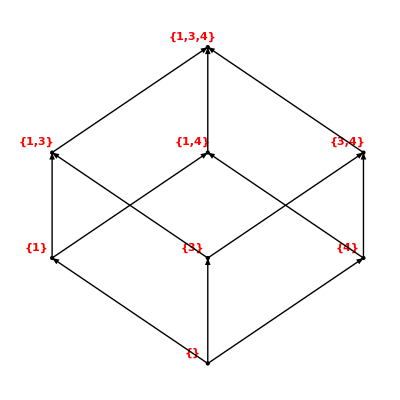

```mathematica
A=X;
R;(*Calculada anteriormente*)
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,
	{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},
	{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],
		{k1,1,Length[R]}
];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,
	Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],
	Point[{k1-(cont/2),j1}]}
];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
	Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

### Ejercicio 8.8.

En el conjunto A={1,2,3,4} se establece la relación binaria
R={(1,1),(2,2),(2,3),(2,4),(3,2),(3,3)(3,4),(4,2),(4,3),(4,4)}
Justificar que es una relación de equivalencia y calcular el conjunto cociente.

```mathematica
A={1,2,3,4};
R={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};
```

```mathematica
AnalisisRB[A,R]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{2,3},{2,4},{3,2},{3,4},{4,2},{4,3}}

R es una relación de equivalencia

R no es relación de orden

```mathematica
COCIENTE[A,R]
```

{{1},{2,3,4}}

### Ejercicio 8.14

Sea X = {a,b,c,d,e,f} junto con la ordenación dada por el siguiente diagrama:
-Graphics-
Sea Y=[b,f,e} y Z={e,b,c,a} subconjuntos de X. Se pide:

```mathematica
X={"a","b","c","d","e","f"};
Y={"b","f","e"};
Z={"e","b","c","a"};
R={{"f","f"},{"f","e"},{"f","d"},{"f","b"},{"f","c"},{"f","a"},
	{"e","e"},{"e","c"},{"e","b"},{"e","a"},
	{"d","d"},{"d","b"},{"d","a"},
	{"b","b"},{"b","a"},{"c","c"},{"a","a"}};
```

a) Cotas superiores e inferiores de Y y de Z . ¿Existen supremo e ínfimo?

```mathematica
COTASSUPERIORES[Y,Z,R]
SUPREMO[Y,Z,R]
```

{}

{}

```mathematica
COTASINFERIORES[Y,Z,R]
INFIMO[Y,Z,R]
```

{f,e}

{e}

b) Máximos y mínimos de Y y Z

```mathematica
MAXIMO[Y,R]
MINIMO[Y,R]
```

{b}

{f}

```mathematica
MAXIMO[Z,R]
MINIMO[Z,R]
```

c) Elementos maximales y minimales de X, Y y Z

```mathematica
MAXIMALES[X,R]
MINIMALES[X,R]
```

{a,c}

{f}

```mathematica
MAXIMALES[Y,R]
MINIMALES[Y,R]
```

{b}

{f}

```mathematica
MAXIMALES[Z,R]
MINIMALES[Z,R]
```

{c,a}

{e}

d) Representar con Mathematica el diagrama de orden X, Y y Z .

Diagrama de orden:

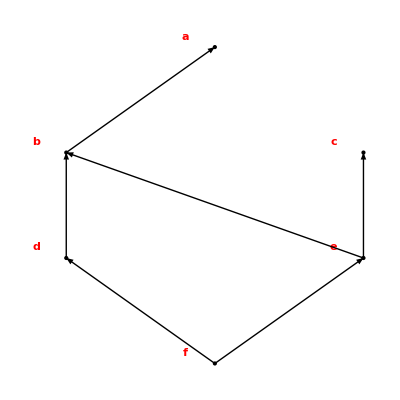

```mathematica
A=X;
R;(*Calculada anteriormente*)
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
	R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,
	FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],
	{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

### Ejercicio 2 de la Extraordinaria 2 del 23/24

Definir una relación de orden en el conjunto X = P ({∅})*𝔹2 verificando que existe un único elemento de X que sea a la vez maximal y minimal . Hacer todas las comprobaciones . Dibujar el diagrama de orden y razonar si X está bien ordenado

```mathematica
A=Subsets[{{}}];
B={0,1};
cartesiano={};
Do[Do[AppendTo[cartesiano,{A[[i]],B[[j]]}],{i,1,Length[A]}];,{j,1,Length[B]}];
X=cartesiano
```

{{{},0},{{{}},0},{{},1},{{{}},1}}

```mathematica
R={ { {{},0},{{},0} }, { {{{}},0},{{{}},0} }, { {{},1}, {{},1} }, { {{{}},1}, {{{}},1} } ,
	{ {{},0},{{{}},0} }, { {{},0},{{},1} }, { {{{}},0},{{},1} }};
	
ORDEN[A_,R_]:=Module[{falloReflexiva,falloAntisimetrica,falloTransitiva},
	falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),
	AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}
];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,
	AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,
		{q,Length[R]}];,{p,Length[R]}
];
If[falloReflexiva=={},Print["R es reflexiva"],
	Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],
	Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],
	Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},
	Print["R es una relación de orden"],Print["R no es relación de orden"]];];

ORDEN[X,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]

MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]

MAXIMALES[X,R]
MINIMALES[X,R]
```

{{{},1},{{{}},1}}

{{{},0},{{{}},1}}

Diagrama de orden:

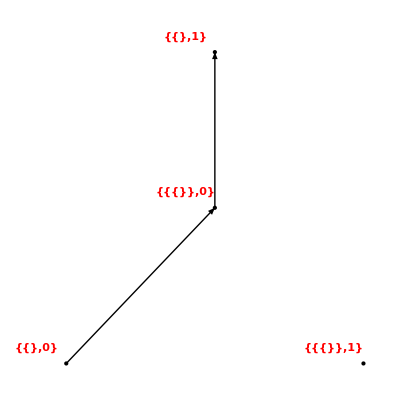

```mathematica
A=X;
R;
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
	R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}
];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,
	FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],
	{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```